```mathematica
H[z_]:= √(.38*(1+z)^3+.7)
```

```mathematica
AlphaD[z_,α_]:= (1+z)^(1-α)/(72/3*^5)Integrate[(1+zp)^(α-2)/H[zp],{zp,0,z}]
```

```mathematica
AlphaDscaled[z_,α_]:= Integrate[(1+zp)^(α-2)/H[zp],{zp,0,z}]
```

```mathematica
AlphaD[1,3]
```

1087.01

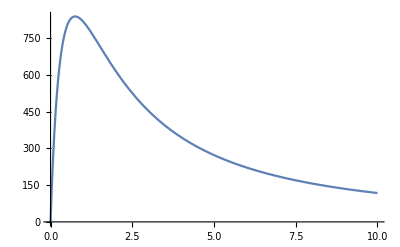

```mathematica
Plot[AlphaD[z,4],{z,0,10}]
```

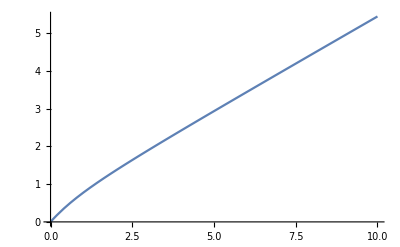

```mathematica
Plot[AlphaD[z,0],{z,0,10}]
```

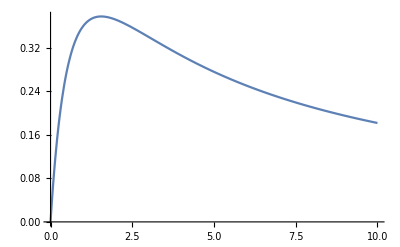

```mathematica
Plot[AlphaD[z,2],{z,0,10}]
```

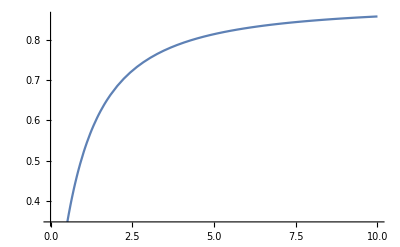

```mathematica
Plot[AlphaD[z,1],{z,0,10}]
```

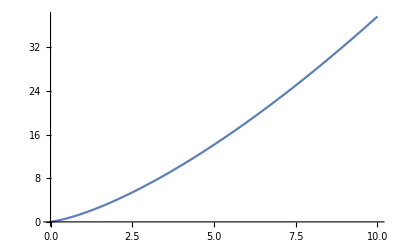

```mathematica
Plot[AlphaDscaled[z,4],{z,0,10}]
```

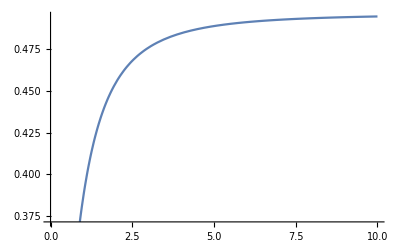

```mathematica
Plot[AlphaDscaled[z,0],{z,0,10}]
```

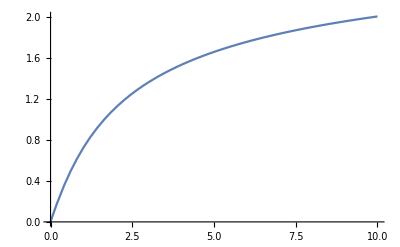

```mathematica
Plot[AlphaDscaled[z,2],{z,0,10}]
```

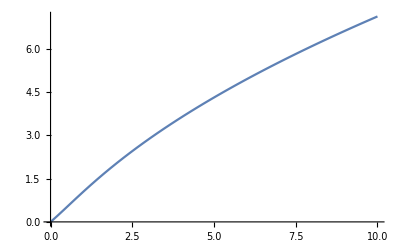

```mathematica
Plot[AlphaDscaled[z,3],{z,0,10}]
```

```mathematica
Plot[AlphaDscaled[z,1],{z,0,10}]
```

-Graphics-

0.0000750838+(8.60336×10^-16)/x^2.-(2.02536×10^-12)/x^1.5+(1.65725×10^-9)/x^1.-(5.61488×10^-7)/x^0.5-0.00355635 x^0.5+1.02483 x^1.-0.450478 x^1.5-0.962485 x^2.

9

5.05799+0.0154011/x^2.-0.204787/x^1.5+1.12149/x^1.-3.22697/x^0.5-3.77556 x^0.5+1.48192 x^1.-0.297552 x^1.5+0.0241459 x^2.

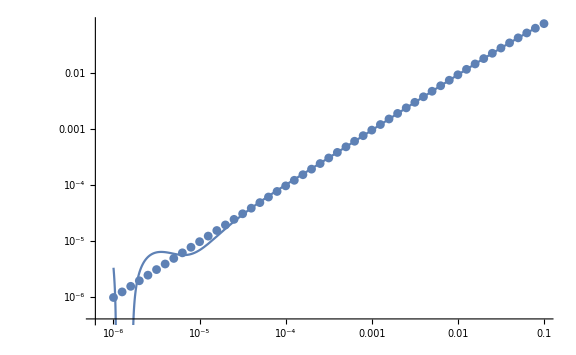

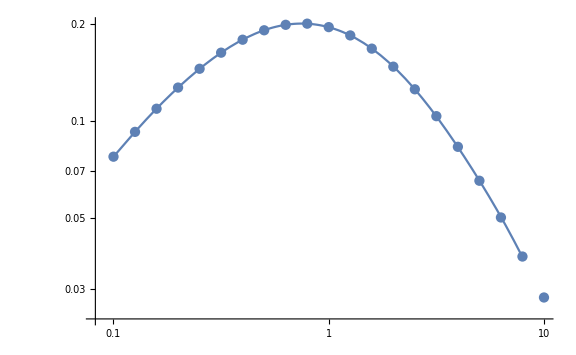

```mathematica
alpha = 4;
Data = Table[{10^x,AlphaD[10^x,alpha]},{x,-6,-1,.1}];
Data2 = Table[{10^x,AlphaD[10^x,alpha]},{x,-1,1,.1}];
(*fit = Fit[Data,Table[x^i,{i,alpha-5,alpha+5,.5}],x]
Length[Table[x^i,{i,alpha-5,alpha+5,.5}]]
fit2 = Fit[Data2,Table[x^i,{i,alpha-5,alpha+5,.5}],x]*)
fit = Fit[Data,Table[x^i,{i,-2,+2,.5}],x]
Length[Table[x^i,{i,-2,+2,.5}]]
fit2 = Fit[Data2,Table[x^i,{i,-2,+2,.5}],x]
Show[ListLogLogPlot[Data],LogLogPlot[fit,{x,Data[[1]][[1]],Data[[Length[Data]-1]][[1]]}],ImageSize->Large]
Show[ListLogLogPlot[Data2],LogLogPlot[fit2,{x,Data2[[1]][[1]],Data2[[Length[Data2]-1]][[1]]}],ImageSize->Large]
```